ExB drift at detector

### describe simplified ExB drift behaviour (radial linear, linear in momentum)

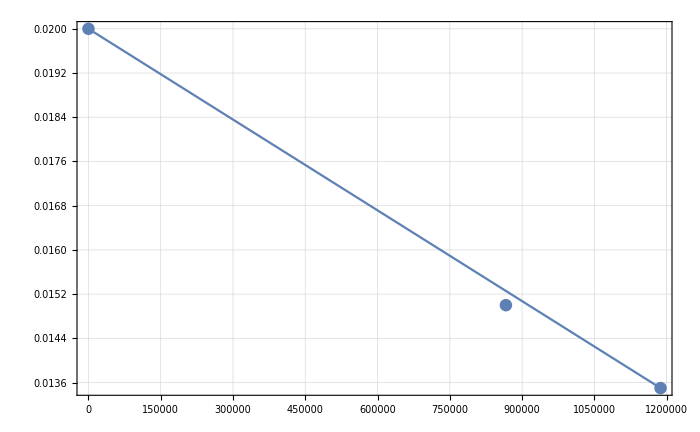

```mathematica
Show[ListPlot[{{0,0.020},{pofTClassic[400,mp],0.015},{pmax,0.0135}}],Plot[-p/pmax*0.0065+0.02,{p,0,pmax}]]
```

### give k also scale so that you can turn it off

### direction given by e_phi with arctan of x and y

```mathematica
Cos[ArcTan[x,y]]
```

x/(√(x^2+y^2))

```mathematica
Sin[ArcTan[x,y]]
```

y/(√(x^2+y^2))

```mathematica
DExB[p_,xGC_,yGC_]:=k[p]*{-yGC,xGC}
```

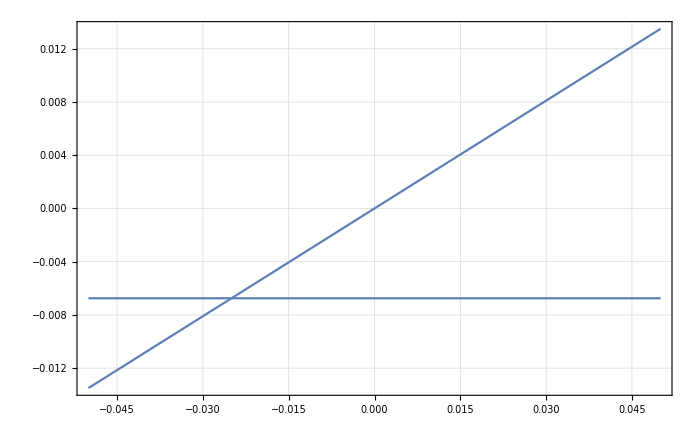

```mathematica
Plot[DExB[1187000,xGC,0.025],{xGC,-0.05,0.05}]
```

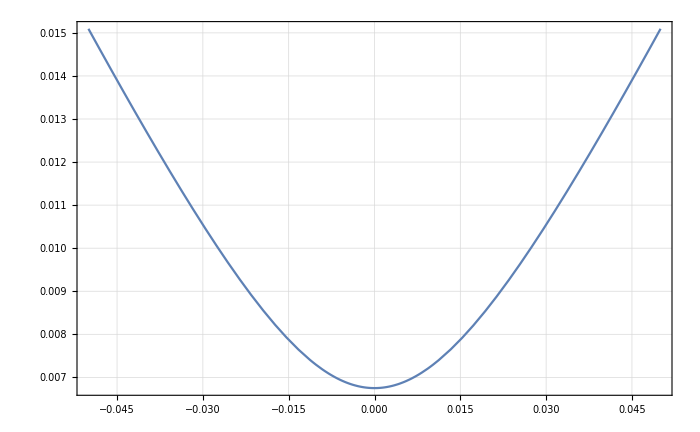

```mathematica
Plot[Norm[DExB[1187000,xGC,0.025]],{xGC,-0.05,0.05}]
```

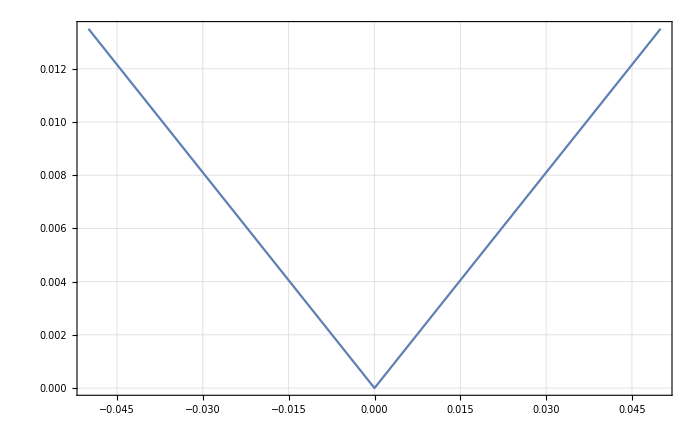

```mathematica
Plot[Norm[DExB[1187000,xGC,0.]],{xGC,-0.05,0.05}]
```

### now we have to make the integrand and get new momentum limitations

```mathematica
Get["ExBDrift/ExBDrift_ProtonTransport.m"]
```

### now get p limits

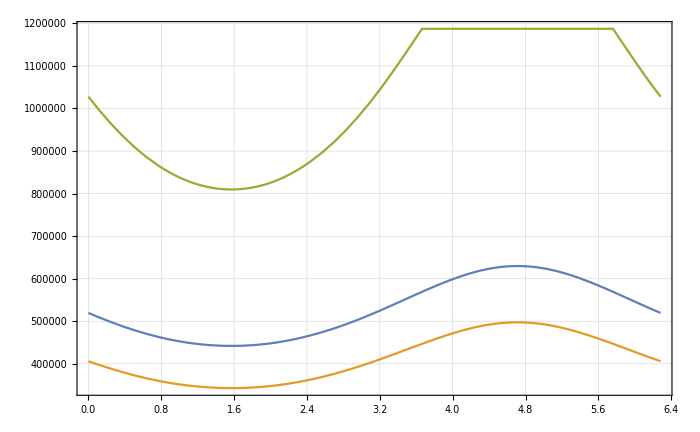

```mathematica
Plot[{pminExBCases[{-0.04,0.01,phi,Pi/4,Pi,0.2,1.,1.},{0.01,0.035,1.},0.00001],
pminExBCases[{-0.04,0.01,phi,Pi/4,Pi,0.2,1.,1.},{0.01,0.035,1.},1],
pmaxExBCases[{-0.04,0.01,phi,Pi/4,Pi,0.2,1.,1.},{0.01,0.035,1.},0.00001]
},{phi,0,2*Pi}]
```

```mathematica
Plot3D[Integrand2DExB[0.,{-0.03,0.005,phi,p,Pi/4,Pi/2,0.2,1./2,1./2},{0.01,0.035,0.,0.,1./2,3},1],
{phi,0,2*Pi},
{
p,
pminExBCases[{-0.03,0.005,phi,Pi/4,Pi/2,0.2,1./2,1./2},{0.01,0.035,1./2},1],
pmaxExBCases[{-0.03,0.005,phi,Pi/4,Pi/2,0.2,1./2,1./2},{0.01,0.035,1./2},1]
},
PlotPoints->12,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[Integrand2DExB[0.,{-0.03,0.005,phi,p,Pi/4,Pi/2,0.2,1./2,1./2},{0.01,0.035,0.,0.,1./2,3},0.0001],
{phi,0,2*Pi},
{
p,
pminExBCases[{-0.03,0.005,phi,Pi/4,Pi/2,0.2,1./2,1./2},{0.01,0.035,1./2},0.0001],
pmaxExBCases[{-0.03,0.005,phi,Pi/4,Pi/2,0.2,1./2,1./2},{0.01,0.035,1./2},0.0001]
},
PlotPoints->12,PlotRange->All]
```

-Graphics3D-

```mathematica
TestIntegration=NIntegrate[
Integrand2DExB[0.,{-0.03,0.005,phi,p,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,0.,0.,1./2,3},1],
{th0,0,Pi/2},
{phi,0,2*Pi},
{p,pminExBCases[{-0.03,0.005,phi,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,1./2},1],pmaxExBCases[{-0.03,0.005,phi,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,1./2},1]},
PrecisionGoal->2
]
```

1.0462

### took 126 s

```mathematica
TestIntegration2=NIntegrate[
Integrand2DExB[0.,{-0.04,0.005,phi,p,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,0.,0.,1./2,3},1],
{th0,0,Pi/2},
{phi,0,2*Pi},
{p,pminExBCases[{-0.04,0.005,phi,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,1./2},1],pmaxExBCases[{-0.04,0.005,phi,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,1./2},1]},
PrecisionGoal->2
]
```

0.227123

```mathematica
t0=AbsoluteTime[];
TestIntegration3=ParallelTable[{
xD,
NIntegrate[
Integrand2DExB[0.,{xD,0.005,phi,p,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,0.,0.,1./2,3},1],
{th0,0,Pi/2},
{phi,0,2*Pi},
{p,pminExBCases[{xD,0.005,phi,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,1./2},1],pmaxExBCases[{xD,0.005,phi,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,1./2},1]},
PrecisionGoal->2
]},{xD,{-0.01,-0.02,-0.03,-0.05}},Method->"FinestGrained"]
t1=AbsoluteTime[];
t1-t0
```

{{-0.01,2.18401},{-0.02,2.37957},{-0.03,1.03008},{-0.05,0.0381058}}

349.89462

```mathematica
(ApertureFunc[0.01,0.035,0.,0.,0.01,0.01,Pi/4,700000,0.2,7]-MonteCarloAperture[0.01,0.035,0.,0.,0.01,0.01,Pi/4,700000,0.2,100])/ApertureFunc[0.01,0.035,0.,0.,0.01,0.01,Pi/4,700000,0.2,7]
```

0.00991544

```mathematica
t0=AbsoluteTime[];
TestIntegration3DuplicateMC=ParallelTable[{
xD,
NIntegrate[
Integrand2DExBMC[0.,{xD,0.005,phi,p,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,0.,0.,1./2,100},1],
{th0,0,Pi/2},
{phi,0,2*Pi},
{p,pminExBCases[{xD,0.005,phi,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,1./2},1],pmaxExBCases[{xD,0.005,phi,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,1./2},1]},
PrecisionGoal->2
]},{xD,{-0.01,-0.02,-0.03,-0.05}},Method->"FinestGrained"]
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{-0.01,2.17918},{-0.02,2.41469},{-0.03,1.04392},{-0.05,0.0361126}}

538.062958

### took 259s

```mathematica
t0=AbsoluteTime[];
TestIntegration3DuplicateMC2=ParallelTable[{
xD,
NIntegrate[
Integrand2DExBMC[0.,{xD,0.005,phi,p,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,0.,0.,1./2,600},1],
{th0,0,Pi/2},
{phi,0,2*Pi},
{p,pminExBCases[{xD,0.005,phi,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,1./2},1],pmaxExBCases[{xD,0.005,phi,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,1./2},1]},
PrecisionGoal->2
]},{xD,{-0.01,-0.02,-0.03,-0.05}},Method->"FinestGrained"]
t1=AbsoluteTime[];
t1-t0
```

{{-0.01,2.17822},{-0.02,2.37875},{-0.03,1.03454},{-0.05,0.0381031}}

144.12439

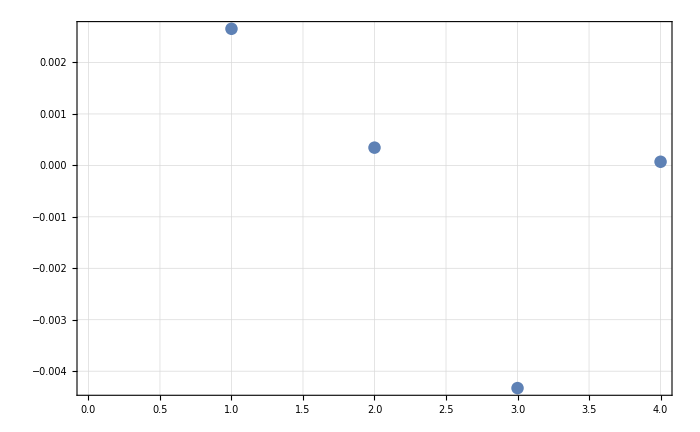

```mathematica
ListPlot[{
(*TestIntegration3[[All,2]]-TestIntegration3DuplicateMC[[All,2]],*)
(TestIntegration3[[All,2]]-TestIntegration3DuplicateMC2[[All,2]])/TestIntegration3[[All,2]]
}]
```

```mathematica
TestIntegration4=ParallelTable[{
xD,
NIntegrate[
Integrand2DExB[0.,{xD,0.005,phi,p,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,0.,0.,1./2,3},1],
{th0,0,Pi/2},
{phi,0,2*Pi},
{p,pminExBCases[{xD,0.005,phi,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,1./2},1],pmaxExBCases[{xD,0.005,phi,th0,Pi/2,0.2,1./2,1./2},{0.01,0.035,1./2},1]},
PrecisionGoal->2
]},{xD,{0,0.004}},Method->"FinestGrained"]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{0,0.14481},{0.004,0.}}

```mathematica
Join[{{-0.03,TestIntegration},{-0.04,TestIntegration2}},TestIntegration3]
```

{{-0.03,1.0462},{-0.04,0.227123},{-0.01,2.17991},{-0.02,2.41388},{-0.05,0.0362255}}

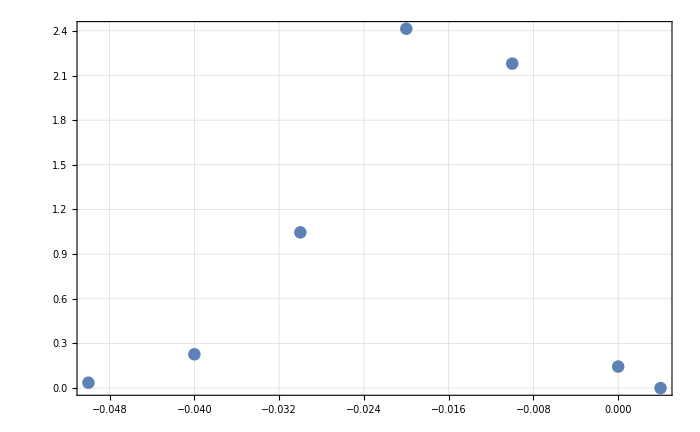

```mathematica
ListPlot[Join[{{-0.03,TestIntegration},{-0.04,TestIntegration2}},TestIntegration3,TestIntegration4]]
```

```mathematica
ClearAll[XYBinData]
```

```mathematica
XYBinDataSmall=Flatten[Table[{xD,yD},{xD,-0.045,-0.005,0.04/(3-1)},{yD,-0.035/2,0.035/2,(0.035)/(2-1)}],1]
```

{{-0.045,-0.0175},{-0.045,0.0175},{-0.025,-0.0175},{-0.025,0.0175},{-0.005,-0.0175},{-0.005,0.0175}}

```mathematica
XYBinDataSmall//Length
```

6

```mathematica
?IntegrationExBMC
```

Global`IntegrationExBMC

IntegrationExBMC[a_?NumericQ,{alpha_?NumericQ,BRxB_?NumericQ,rRxB_?NumericQ,rD_?NumericQ,rF_?NumericQ},{xA_?NumericQ,yA_?NumericQ,xOff_?NumericQ,yOff_?NumericQ,rA_?NumericQ,MCSteps_?NumericQ},kscale_?NumericQ,BinN_?NumericQ,BinList_List,IntPrec_]:=ParallelTable[NIntegrate[Integrand2DExBMC[a,{BinList⟦bin,1⟧,BinList⟦bin,2⟧,phi,p,th0,alpha,BRxB,rRxB,rD},{xA,yA,xOff,yOff,rA,MCSteps},kscale],{th0,0,thetamax[rF]},{phi,0,2 π},{p,pminExBCases[{BinList⟦bin,1⟧,BinList⟦bin,2⟧,phi,th0,alpha,BRxB,rRxB,rD},{xA,yA,xOff,yOff,rA},kscale],pmaxExBCases[{BinList⟦bin,1⟧,BinList⟦bin,2⟧,phi,th0,alpha,BRxB,rRxB,rD},{xA,yA,xOff,yOff,rA},kscale]},PrecisionGoal→IntPrec],{bin,1,BinN},Method→FinestGrained]

```mathematica
t0=AbsoluteTime[];
TestInt2DExB6BinsMC100=IntegrationExBMC[-0.103,{Pi/2,0.2,1./2,1./2,1.},{0.01,0.035,0.,0.,1./2,100},1,6,XYBinDataSmall,2];
t1=AbsoluteTime[];
t1-t0
```

$Aborted

8.161836

```mathematica
t0=AbsoluteTime[];
TestInt2DExB6BinsMCPrec3=IntegrationExBMC[-0.103,{Pi/2,0.2,1./2,1./2,1.},{0.01,0.035,0.,0.,1./2,600},1,6,XYBinDataSmall,3];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

3604.402915

```mathematica
t0=AbsoluteTime[];
TestInt2DExB6BinsMCless=IntegrationExBMC[-0.103,{Pi/2,0.2,1./2,1./2,1.},{0.01,0.035,0.,0.,1./2,100},1,6,XYBinDataSmall,2];
t1=AbsoluteTime[];
t1-t0
```

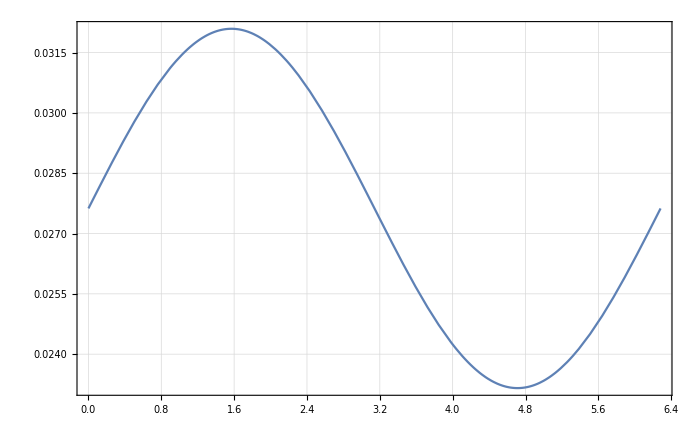

```mathematica
Plot[x0fromExB[k[700000,1],-0.01,0.,rG[700000,Pi/8,0.2],phi,-700000*Pi/0.2/c],{phi,0,2*Pi}]
```

```mathematica
XYBinDataXOff=Flatten[Table[{xD,yD},{xD,-0.025,0.03,0.055/(10-1)},{yD,-0.035/2-0.01,0.035/2+0.01,(0.035+0.02)/(5-1)}],1]
```

{{-0.025,-0.0275},{-0.025,-0.01375},{-0.025,0.},{-0.025,0.01375},{-0.025,0.0275},{-0.0188889,-0.0275},{-0.0188889,-0.01375},{-0.0188889,0.},{-0.0188889,0.01375},{-0.0188889,0.0275},{-0.0127778,-0.0275},{-0.0127778,-0.01375},{-0.0127778,0.},{-0.0127778,0.01375},{-0.0127778,0.0275},{-0.00666667,-0.0275},{-0.00666667,-0.01375},{-0.00666667,0.},{-0.00666667,0.01375},{-0.00666667,0.0275},{-0.000555556,-0.0275},{-0.000555556,-0.01375},{-0.000555556,0.},{-0.000555556,0.01375},{-0.000555556,0.0275},{0.00555556,-0.0275},{0.00555556,-0.01375},{0.00555556,0.},{0.00555556,0.01375},{0.00555556,0.0275},{0.0116667,-0.0275},{0.0116667,-0.01375},{0.0116667,0.},{0.0116667,0.01375},{0.0116667,0.0275},{0.0177778,-0.0275},{0.0177778,-0.01375},{0.0177778,0.},{0.0177778,0.01375},{0.0177778,0.0275},{0.0238889,-0.0275},{0.0238889,-0.01375},{0.0238889,0.},{0.0238889,0.01375},{0.0238889,0.0275},{0.03,-0.0275},{0.03,-0.01375},{0.03,0.},{0.03,0.01375},{0.03,0.0275}}

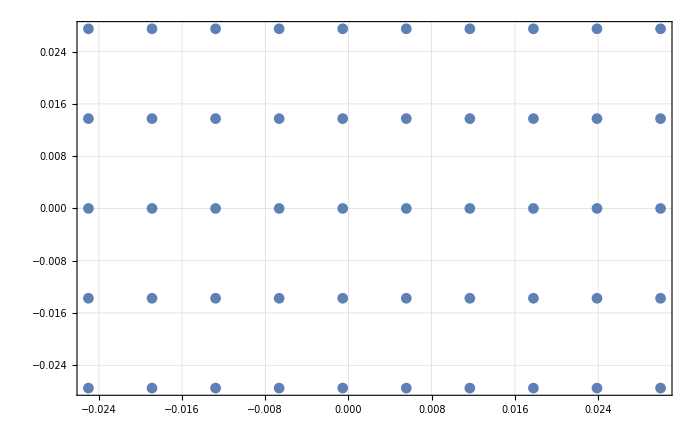

```mathematica
ListPlot[XYBinDataXOff]
```

```mathematica
t0=AbsoluteTime[];
TestInt2DExB50BinsXOff=IntegrationExBMC[0.,{Pi/2,0.2,1./2,1./2,1.},{0.01,0.035,0.025,0.,1./2,600},1,50,XYBinDataXOff];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.019285 and 0.000107434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000359353 and 1.95923×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

16699.0522

### for prec 2, 12436 seconds (50 bins), without xOffset

```mathematica
12436/3600.
```

3.45444

```mathematica
ListPlot3D[Transpose[{XYBinData[[All,1]],XYBinData[[All,2]],TestInt2DExB50Bins}]]
```

-Graphics3D-

```mathematica
t0=AbsoluteTime[];
TestInt2DnoExB50BinsXOff=IntegrationExBMC[0.,{Pi/2,0.2,1./2,1./2,1.},{0.01,0.035,0.025,0.,1./2,600},0.00001,50,XYBinDataXOff];
t1=AbsoluteTime[];
t1-t0
```

### we can also get a limit on phi with the y aspect in aperture -> no, we can’t because it would depend on momentum p! but we could give it as bool

```mathematica
phiminExB[{xD_?NumericQ,yD_?NumericQ,p_?NumericQ,th0_,BRxB_,rRxB_,rD_},{yA_,yOff_,rA_},kscale_]=Re[Solve[y0fromExB[k[p,kscale],xD,yD,rG[p,theta2[th0,rD],rD*BRxB/rRxB],phi]==-yA/2-rG[p,theta2[th0,rA],rA*BRxB/rRxB]+yOff,phi][[All,1,2]]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
phimaxExB[{xD_?NumericQ,yD_?NumericQ,p_?NumericQ,th0_,BRxB_,rRxB_,rD_},{yA_,yOff_,rA_},kscale_]=Re[Solve[y0fromExB[k[p,kscale],xD,yD,rG[p,theta2[th0,rD],rD*BRxB/rRxB],phi]==yA/2+rG[p,theta2[th0,rA],rA*BRxB/rRxB]+yOff,phi][[All,1,2]]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
phiminExB[{-0.01,0.,1000000,Pi/4,0.2,1.,1.},{0.035,0.,1.},1]
```

{-3.14159,3.14159}

```mathematica
phimaxExB[{-0.03,0.,500000,Pi/4,0.2,1.,1.},{0.035,0.,1.},1]
```

{0.,0.}

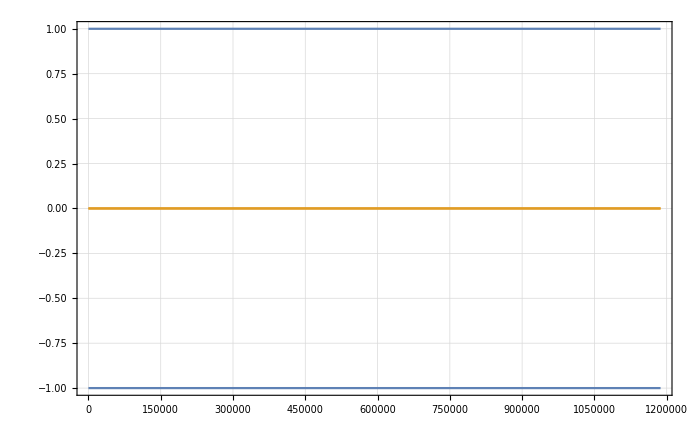

```mathematica
Plot[
{
phiminExB[{-0.03,0.,p,Pi/8,0.2,1.,1.},{0.035,0.,1.},1]/Pi,
phimaxExB[{-0.03,0.,p,Pi/8,0.2,1.,1.},{0.035,0.,1.},1]/Pi
},{p,0,pmax}]
```

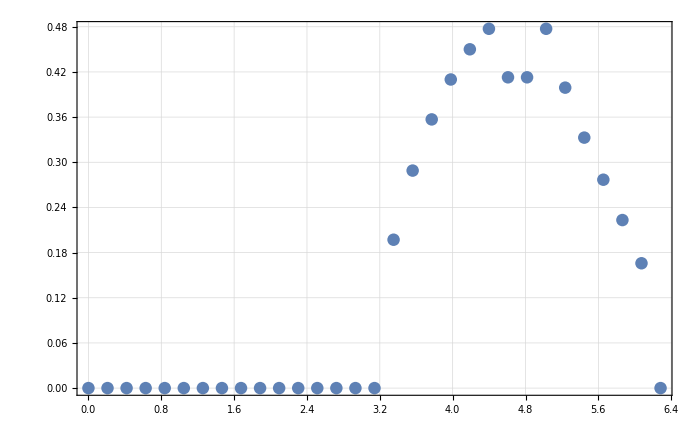

```mathematica
ListPlot[Table[{phi,ApertureFunc[0.01,0.035,0.025,0.,x0fromExB[k[900000,1],-0.01,0.,rG[900000,theta2[Pi/4,1],1*0.2/1],phi,-D1stSimple[900000,Pi,0.2,Pi/4,1]],y0fromExB[k[900000,1],-0.01,0.,rG[900000,theta2[Pi/4,1],1*0.2/1],phi],theta2[Pi/4,1],900000,0.2,3]},{phi,0,2*Pi,2*Pi/30}]]
```

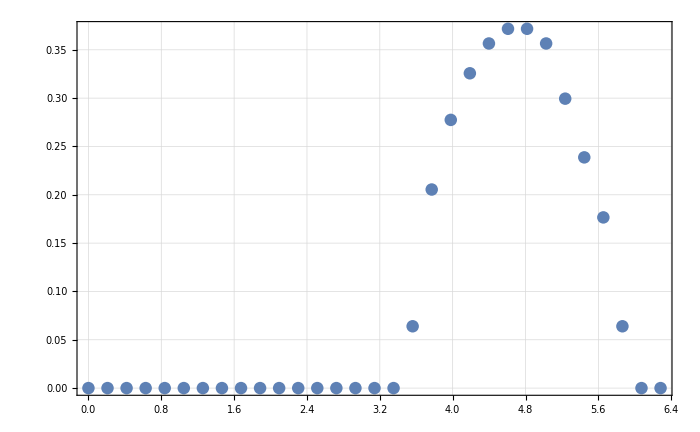

```mathematica
ListPlot[Table[{phi,ApertureFunc[0.01,0.035,0.025,0.,x0fromExB[k[1000000,1],-0.01,0.,rG[1000000,theta2[Pi/4,1],1*0.2/1],phi,-D1stSimple[1000000,Pi,0.2,Pi/4,1]],y0fromExB[k[1000000,1],-0.01,0.,rG[1000000,theta2[Pi/4,1],1*0.2/1],phi],theta2[Pi/4,1],1000000,0.2,3]},{phi,0,2*Pi,2*Pi/30}]]
```

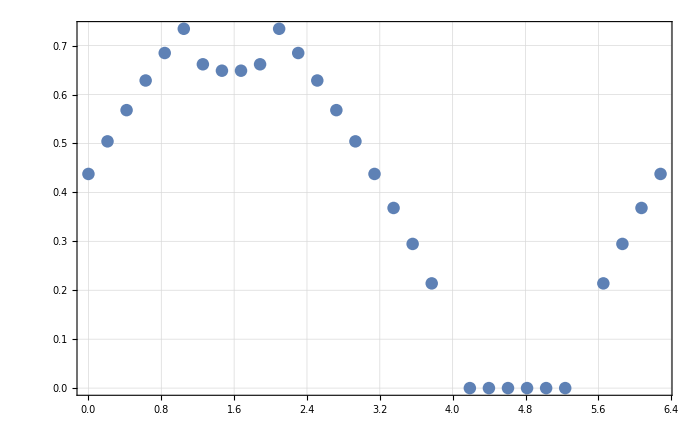

```mathematica
ListPlot[Table[{phi,ApertureFunc[0.01,0.035,0.025,0.,x0fromExB[k[500000,1],-0.01,0.,rG[500000,theta2[Pi/4,1],1*0.2/1],phi,-D1stSimple[500000,Pi,0.2,Pi/4,1]],y0fromExB[k[500000,1],-0.01,0.,rG[500000,theta2[Pi/4,1],1*0.2/1],phi],theta2[Pi/4,1],500000,0.2,3]},{phi,0,2*Pi,2*Pi/30}]]
```